```mathematica
□_□
```

# Insights from 2016-2020 car accident data in the UK

By Full-time students group 6:  BALAJI KOLLA ,  SNEHA SUSAN JOJI ,  DOROTA KUZMA,  AJAY MADHUKAR DHAKNE,  DEREK KWEKU DEGBEDZUI, STANLEY AMOAKO

# Importing

## For long term data analysis

### Importing the file “Road Safety - Casualties last 5 years“:

```mathematica
FullAccidents=Import["C:\\Users\\Lenovo\\Desktop\\uni masters\\introduction to data science\\group project\\dft-road-casualty-statistics-accident-last-5-years.csv",{"Dataset"}];
```

## For short term data analysis

### Importing data using SemanticImport function to automatically convert the data from the date column in the original CSV file into Dataset objects:

Importing accidents data from last 5 years from file “Road Safety - Accidents last 5 years”:

```mathematica
fullaccidents=SemanticImport["C:\\Users\\Lenovo\\Documents\\group project data\\dft-road-casualty-statistics-accident-last-5-years.csv"];
```

Importing accidents data from 2020 from file “Road Safety Data - Accidents 2020”:

```mathematica
only2020= SemanticImport["C:\\Users\\Lenovo\\Documents\\group project data\\dft-road-casualty-statistics-accident-2020.csv"];
```

Importing accidents data from 2019 from file “Road Safety Data - Accidents 2019”:

```mathematica
only2019=SemanticImport["C:\\Users\\Lenovo\\Documents\\group project data\\dft-road-casualty-statistics-accident-2019.csv"];
```

The same “Road Safety - Casualties last 5 years” file was uploaded twice for ease of analysis between different researchers.

# Pre-processing

## For long term data analysis

### Accident year, severity, weather condition, speed limit

Selecting  data  from the accident_year and accident_severity columns about all accidents in years 2016-2020:

```mathematica
accidentsbasedonseverityyearly=FullAccidents[[2;;,{2,9}]];
```

Selecting data from the accident_severity and weather_conditions columns about all accidents in years 2016-2020:

```mathematica
accidentsbasedonseverityweather=FullAccidents[[2;;,{9,29}]];
```

Selecting data from the accident_severity and speed_limit columns about all accidents in years 2016-2020:

```mathematica
Speedlimitdata=FullAccidents[[2;;,{9,21}]];
```

Selecting data from the accident_severity column for all accidents in years 2016-2020:

```mathematica
AccSev=FullAccidents[[2;;597973, 9]]; TableView[AccSev];
```

Same as above but only for 
2016:

```mathematica
AccSev16=FullAccidents[[2;;136621, 9]]; TableView[AccSev16];
```

2017 :

```mathematica
AccSev17=FullAccidents[[136622;;266603, 9]]; TableView[AccSev17];
```

2018 :

```mathematica
AccSev18=FullAccidents[[266604;;389238, 9]]; TableView[AccSev18];
```

2019:

```mathematica
AccSev19=FullAccidents[[389239;;506774, 9]]; TableView[AccSev19];
```

2020:

```mathematica
AccSev20=FullAccidents[[506775;;597973, 9]]; TableView[AccSev20];
```

Selecting data from the weather_condition column from all years:

```mathematica
weatheracc=FullAccidents[[2;;,29]];
```

Selecting accidents by severity and lighting, from the accident_severity and light_condition column:

```mathematica
SeverityLightC=FullAccidents[[2;;597974, {9,28}]]; TableView[SeverityLightC];
```

### Road type, light condition, day of week

Selecting accidents due to different types of roads from all years, using column road_type :

```mathematica
RoadT=FullAccidents[[2;;597974, {2,20}]]; TableView[RoadT];
```

Selecting accidents by different light conditions, using column  ligh_conditions :

```mathematica
DuetoLightC=FullAccidents[[2;;597974, {2,28}]]; TableView[DuetoLightC];
```

Selecting accidents on different days of the week from all years, using column day_of_week :

```mathematica
daysoftheweek=FullAccidents[[2;;597973,13]];
```

Selecting accidents by different road types and severity, using column road_type and accident_severity :

```mathematica
SeverityRoadType=FullAccidents[[2;;597974, {9,20}]]; TableView[SeverityRoadType];
```

## For short term data analysis

### Years 2016 - 2020

Selecting the columns accident_year and date for all the accidents in years 2016-2020 and counting them using Tally:

```mathematica
yearanddate=
fullaccidents[[All,{"accident_year","date"}]];
```

```mathematica
countedYearandDate=Tally[SortBy[yearanddate,"date"]];
```

Calculating the mean number of accidents in the early days in years 2016, 2017, 2018. As 2016 was a leap year the mean was calculated from 85 days, for 2017 and 2018 it was calculated from 84 days.

```mathematica
first85in2016=countedYearandDate[[;;85,All]];
```

```mathematica
mean2016first=Mean[first85in2016[[All,2]]]//N
```

368.435

```mathematica
first85in2017=countedYearandDate[[367;;450,All]];
```

```mathematica
mean2017first=Mean[countedYearandDate[[All,2]]]//N
```

327.298

```mathematica
first85in2018=countedYearandDate[[732;;815,All]];
```

```mathematica
mean2018first=Mean[countedYearandDate[[All,2]]]//N
```

327.298

Calculating the mean number of accidents in the 85 days after March 26th in years 2016, 2017, 2018.

```mathematica
later85in2016=countedYearandDate[[86;;170,All]];
```

```mathematica
mean2016=Mean[later85in2016[[All,2]]]//N
```

359.612

```mathematica
later85in2017=countedYearandDate[[451;;535,All]];
```

```mathematica
mean2017=Mean[later85in2017[[All,2]]]//N
```

345.506

```mathematica
later85in2018=countedYearandDate[[816;;900,All]];
```

```mathematica
mean2018=Mean[later85in2018[[All,2]]]//N
```

329.071

This is for later analysis of the effect of lockdown on the number of accidents. 
The means for 85 first days and 85 days after March 26th in 2019 and 2020 are calculated separately later.

### Year 2019 and 2020

Choosing only the date column from the dataset to get dates for all accidents in 2020, same for 2019:

```mathematica
dates2020=only2020[[;;,"date"]];
```

```mathematica
dates2019= only2019[[;;,"date"]];
```

Sorting the dates:

```mathematica
sorted2020=Sort[dates2020];
```

```mathematica
sorted2019=Sort[dates2019];
```

Counting the number of accidents on each day of the year:

```mathematica
dailyaccidents2020=Tally[sorted2020];
```

```mathematica
dailyaccidents2019= Tally[sorted2019];
```

#### Pre-processing for before and after lockdown analysis in 2020:

Selecting the number of accidents for the first 85 days and the 85 days after March 26th in 2020, converting to normal expression.

```mathematica
first85in2020=dailyaccidents2020[[;;85,2]]//Normal
```

{196,222,238,236,154,255,303,301,340,397,237,202,370,395,374,317,396,357,283,386,399,295,332,381,267,233,333,356,337,338,361,289,229,290,316,337,426,391,292,188,290,298,352,328,318,246,225,287,305,242,272,304,217,201,272,326,347,327,328,303,237,334,324,310,347,411,254,238,315,265,300,297,277,234,185,244,205,195,196,206,175,161,171,99,104}

```mathematica
second85in2020=dailyaccidents2020[[86;;170,2]]//Normal
```

{96,113,55,46,58,99,78,89,81,84,78,98,110,88,113,108,115,83,84,134,121,113,100,86,98,108,125,148,132,166,144,133,110,135,103,133,156,146,83,125,147,171,176,151,156,99,123,162,150,177,197,161,157,179,194,252,200,214,179,188,208,205,231,239,268,266,239,240,238,175,196,234,183,169,161,171,190,196,198,235,178,215,230,229,241}

Selecting the number of accidents for the first 84 days and the 85 days after March 26th in 2019, converting to normal expression .

```mathematica
first85in2019=dailyaccidents2019[[;;84,2]]//Normal
```

{231,193,217,233,194,190,309,351,381,351,341,282,176,319,348,370,396,327,236,205,325,432,367,327,375,258,205,358,350,412,312,318,294,257,336,302,324,347,348,266,235,309,300,328,392,401,275,247,282,307,296,323,327,328,284,360,374,369,309,305,286,192,312,363,333,307,390,263,225,322,314,289,318,327,267,258,285,285,327,303,318,280,294,336}

```mathematica
second85in2019=dailyaccidents2019[[85;;169,2]]//Normal
```

{332,309,331,415,314,227,312,350,348,348,333,253,249,265,273,330,327,303,284,198,277,241,299,304,305,370,293,242,298,317,314,344,268,221,283,350,309,342,366,307,251,195,317,340,297,349,297,287,383,385,404,380,288,266,216,296,372,349,396,403,305,225,210,302,298,324,299,320,243,321,348,341,384,400,297,263,347,330,344,324,345,312,279,311,339}

# Data analysis

## Long term analysis

### Severity of accident

Making a Line Plot of the number of accidents each year between 2016-2020 based on severity:

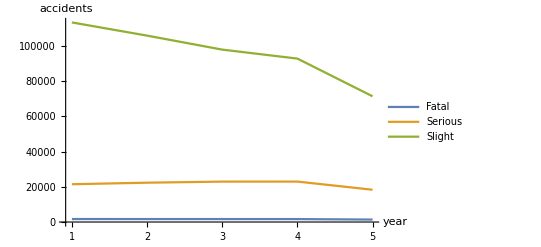

```mathematica
slightseveritynbyyear=ListLinePlot[{{Count[accidentsbasedonseverityyearly,{2016,1}],Count[accidentsbasedonseverityyearly,{2017,1}],Count[accidentsbasedonseverityyearly,{2018,1}],Count[accidentsbasedonseverityyearly,{2019,1}],Count[accidentsbasedonseverityyearly,{2020,1}]},{Count[accidentsbasedonseverityyearly,{2016,2}],Count[accidentsbasedonseverityyearly,{2017,2}],Count[accidentsbasedonseverityyearly,{2018,2}],Count[accidentsbasedonseverityyearly,{2019,2}],Count[accidentsbasedonseverityyearly,{2020,2}]},{Count[accidentsbasedonseverityyearly,{2016,3}],Count[accidentsbasedonseverityyearly,{2017,3}],Count[accidentsbasedonseverityyearly,{2018,3}],Count[accidentsbasedonseverityyearly,{2019,3}],Count[accidentsbasedonseverityyearly,{2020,3}]}},AxesLabel->{"year","accidents"},PlotLegends->{"Fatal","Serious","Slight"},PlotRange->All]
```

Making a bar chart of total Fatal accidents in years 2016-2020:

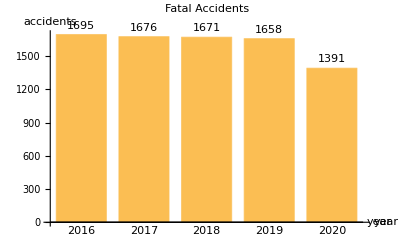

```mathematica
accidentsbasedonseverityFatal=BarChart[{Count[accidentsbasedonseverityyearly,{2016,1}],Count[accidentsbasedonseverityyearly,{2017,1}],Count[accidentsbasedonseverityyearly,{2018,1}],Count[accidentsbasedonseverityyearly,{2019,1}],Count[accidentsbasedonseverityyearly,{2020,1}]}
,AxesLabel->{"year","accidents"},LabelingFunction->(Placed[Row[{#}],Above]&),BarSpacing->Medium,
ChartLabels->{Placed[{"2016","2017","2018","2019","2020"},Below]},PlotLabel->"Fatal Accidents"]
```

Bar chart of total Serious accidents in years 2016-2020:

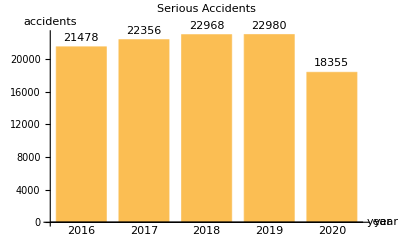

```mathematica
accidentsbasedonseveritySerious=BarChart[{Count[accidentsbasedonseverityyearly,{2016,2}],Count[accidentsbasedonseverityyearly,{2017,2}],Count[accidentsbasedonseverityyearly,{2018,2}],Count[accidentsbasedonseverityyearly,{2019,2}],Count[accidentsbasedonseverityyearly,{2020,2}]}
,AxesLabel->{"year","accidents"},LabelingFunction->(Placed[Row[{#}],Above]&),BarSpacing->Medium,
ChartLabels->{Placed[{"2016","2017","2018","2019","2020"},Below]},PlotLabel->"Serious Accidents"]
```

bar chart of total Slight accidents in years 2016-2020:

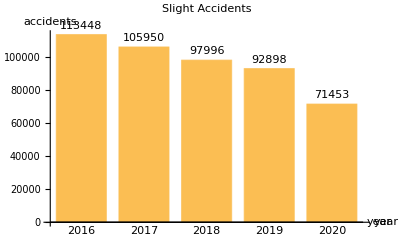

```mathematica
accidentsbasedonseveritySlight=BarChart[{Count[accidentsbasedonseverityyearly,{2016,3}],Count[accidentsbasedonseverityyearly,{2017,3}],Count[accidentsbasedonseverityyearly,{2018,3}],Count[accidentsbasedonseverityyearly,{2019,3}],Count[accidentsbasedonseverityyearly,{2020,3}]}
,AxesLabel->{"year","accidents"},LabelingFunction->(Placed[Row[{#}],Above]&),BarSpacing->Medium,
ChartLabels->{Placed[{"2016","2017","2018","2019","2020"},Below]},PlotLabel->"Slight Accidents"]
```

### Severity and weather condition

Fatal  severity based on type of weather  where the accident  took place in all years

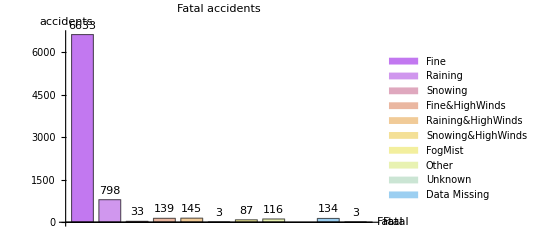

```mathematica
Fatalbyweather=
BarChart[{{Count[accidentsbasedonseverityweather,{1,1}],Count[accidentsbasedonseverityweather,{1,2}],Count[accidentsbasedonseverityweather,{1,3}],Count[accidentsbasedonseverityweather,{1,4}],Count[accidentsbasedonseverityweather,{1,5}],Count[accidentsbasedonseverityweather,{1,6}],Count[accidentsbasedonseverityweather,{1,7}],Count[accidentsbasedonseverityweather,{1,8}],,Count[accidentsbasedonseverityweather,{1,9}],Count[accidentsbasedonseverityweather,{1,-1}]}},AxesLabel->{"Fatal","accidents"},LabelingFunction->(Placed[Row[{#}],Above]&),BarSpacing->Medium, ChartStyle->"Pastel",ChartLegends->{"Fine","Raining","Snowing","Fine&HighWinds","Raining&HighWinds","Snowing&HighWinds","FogMist","Other","Unknown","Data Missing"},PlotLabel->"Fatal accidents"]
```

Serious  severity based on type of weather  where the accident took place in all years

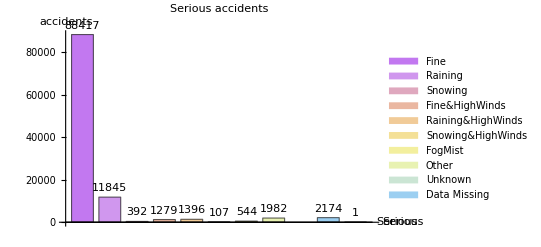

```mathematica
Seriousbyweather=BarChart[{{Count[accidentsbasedonseverityweather,{2,1}],Count[accidentsbasedonseverityweather,{2,2}],Count[accidentsbasedonseverityweather,{2,3}],Count[accidentsbasedonseverityweather,{2,4}],Count[accidentsbasedonseverityweather,{2,5}],Count[accidentsbasedonseverityweather,{2,6}],Count[accidentsbasedonseverityweather,{2,7}],Count[accidentsbasedonseverityweather,{2,8}],,Count[accidentsbasedonseverityweather,{2,9}],Count[accidentsbasedonseverityweather,{2,-1}]}},AxesLabel->{"Serious","accidents"},LabelingFunction->(Placed[Row[{#}],Above]&),BarSpacing->Medium, ChartStyle->"Pastel",ChartLegends->{"Fine","Raining","Snowing","Fine&HighWinds","Raining&HighWinds","Snowing&HighWinds","FogMist","Other","Unknown","Data Missing"},PlotLabel->"Serious accidents"]
```

Slight  severity based on type of weather where the accident took place in all years

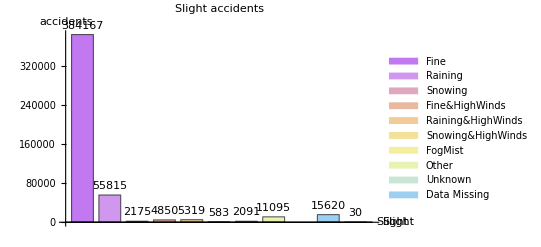

```mathematica
Slightbyweather=BarChart[{{Count[accidentsbasedonseverityweather,{3,1}],Count[accidentsbasedonseverityweather,{3,2}],Count[accidentsbasedonseverityweather,{3,3}],Count[accidentsbasedonseverityweather,{3,4}],Count[accidentsbasedonseverityweather,{3,5}],Count[accidentsbasedonseverityweather,{3,6}],Count[accidentsbasedonseverityweather,{3,7}],Count[accidentsbasedonseverityweather,{3,8}],,Count[accidentsbasedonseverityweather,{3,9}],Count[accidentsbasedonseverityweather,{3,-1}]}},AxesLabel->{"Slight","accidents"},LabelingFunction->(Placed[Row[{#}],Above]&),BarSpacing->Medium, ChartStyle->"Pastel",ChartLegends->{"Fine","Raining","Snowing","Fine&HighWinds","Raining&HighWinds","Snowing&HighWinds","FogMist","Other","Unknown","Data Missing"},PlotLabel->"Slight accidents"]
```

### Only weather condition during the accident for all years 2016-2020:

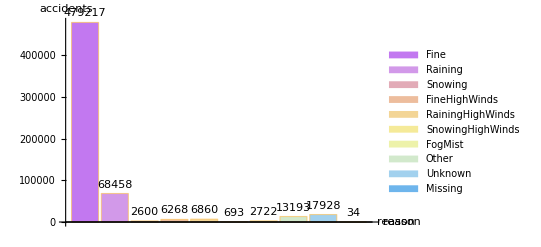

```mathematica
totalweatheracc=BarChart[{Count[weatheracc,1],Count[weatheracc,2],Count[weatheracc,3],Count[weatheracc,4],Count[weatheracc,5],Count[weatheracc,6],Count[weatheracc,7],Count[weatheracc,8],Count[weatheracc,9],Count[weatheracc,-1]},AxesLabel->{"reason","accidents"},LabelingFunction->(Placed[Row[{#}],Above]&),ChartStyle->"Pastel",ChartLegends->{"Fine","Raining","Snowing","FineHighWinds","RainingHighWinds","SnowingHighWinds","FogMist","Other","Unknown","Missing"}]
```

### Severity and speed limit

Bar chart of Fatal accidents based on the Speed limit in the location of the accident:

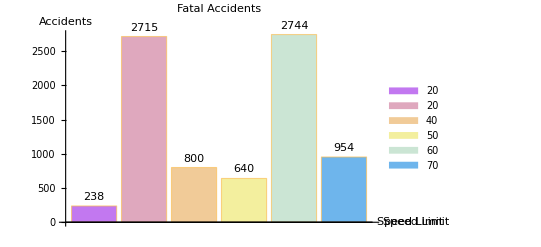

```mathematica
speedlimitfatal=BarChart[{Count[Speedlimitdata,{1,20}],Count[Speedlimitdata,{1,30}],Count[Speedlimitdata,{1,40}],Count[Speedlimitdata,{1,50}],Count[Speedlimitdata,{1,60}],Count[Speedlimitdata,{1,70}]},LabelingFunction->(Placed[Row[{#}],Above]&),ChartStyle->"Pastel",ChartLegends->{"20","20","40","50","60","70"},AxesLabel->{"Speed Limit","Accidents"},PlotLabel->"Fatal Accidents"]
```

Bar chart of Serious accidents based on the Speed limit in the location of the accident :

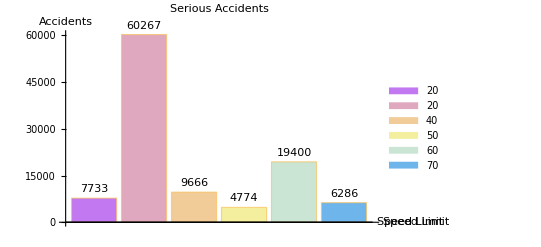

```mathematica
speedlimitserious=BarChart[{Count[Speedlimitdata,{2,20}],Count[Speedlimitdata,{2,30}],Count[Speedlimitdata,{2,40}],Count[Speedlimitdata,{2,50}],Count[Speedlimitdata,{2,60}],Count[Speedlimitdata,{2,70}]},LabelingFunction->(Placed[Row[{#}],Above]&),ChartStyle->"Pastel",ChartLegends->{"20","20","40","50","60","70"},AxesLabel->{"Speed Limit","Accidents"},PlotLabel->"Serious Accidents"]
```

Bar chart of Slight accidents based on the Speed limit in the location of the accident :

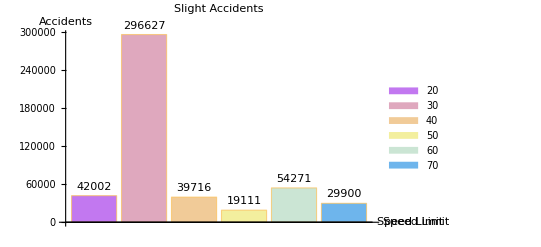

```mathematica
speedlimitslight=BarChart[{Count[Speedlimitdata,{3,20}],Count[Speedlimitdata,{3,30}],Count[Speedlimitdata,{3,40}],Count[Speedlimitdata,{3,50}],Count[Speedlimitdata,{3,60}],Count[Speedlimitdata,{3,70}]},LabelingFunction->(Placed[Row[{#}],Above]&),ChartStyle->"Pastel",ChartLegends->{"20","30","40","50","60","70"},AxesLabel->{"Speed Limit","Accidents"},PlotLabel->"Slight Accidents"]
```

### Severity of accident

Counting the number of car accidents of each severity - Fatal, Serious, Slight- in years 2016-2020, and demonstrating  the counts:

```mathematica
FatalAcc=Count[AccSev,1]
```

8091

```mathematica
SeriousAcc=Count[AccSev,2]
```

108137

```mathematica
SlightAcc=Count[AccSev,3]
```

481744

```mathematica
Total[{FatalAcc,SeriousAcc,SlightAcc}]
```

597972

```mathematica
data={{FatalAcc,2,3},{SeriousAcc,1,2},{SlightAcc,2,1}};
SectorChart3D[data,ChartLabels->{"Fatal","Serious","Slight"}]
```

-Graphics3D-

### Accident road type

Road types for all accidents in years 2016-2020:

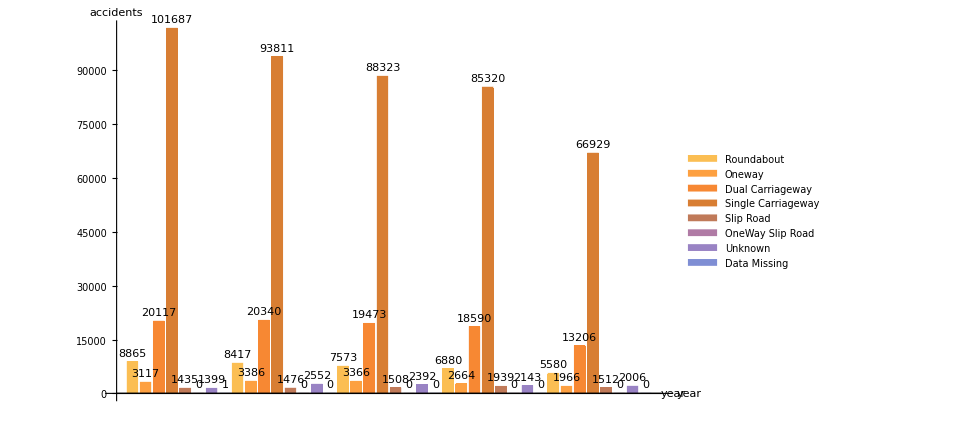

```mathematica
AccidentsRoadType=BarChart[{{Count[RoadT,{2016,1}],Count[RoadT,{2016,2}],Count[RoadT,{2016,3}],Count[RoadT,{2016,6}],Count[RoadT,{2016,7}],Count[RoadT,{2016,12}],Count[RoadT,{2016,9}],Count[RoadT,{2016,-1}]},{Count[RoadT,{2017,1}],Count[RoadT,{2017,2}],Count[RoadT,{2017,3}],Count[RoadT,{2017,6}],Count[RoadT,{2017,7}],Count[RoadT,{2017,12}],Count[RoadT,{2017,9}],Count[RoadT,{2017,-1}]},{Count[RoadT,{2018,1}],Count[RoadT,{2018,2}],Count[RoadT,{2018,3}],Count[RoadT,{2018,6}],Count[RoadT,{2018,7}],Count[RoadT,{2018,12}],Count[RoadT,{2018,9}],Count[RoadT,{2018,-1}]},{Count[RoadT,{2019,1}],Count[RoadT,{2019,2}],Count[RoadT,{2019,3}],Count[RoadT,{2019,6}],Count[RoadT,{2019,7}],Count[RoadT,{2019,12}],Count[RoadT,{2019,9}],Count[RoadT,{2019,-1}]},{Count[RoadT,{2020,1}],Count[RoadT,{2020,2}],Count[RoadT,{2020,3}],Count[RoadT,{2020,6}],Count[RoadT,{2020,7}],Count[RoadT,{2020,12}],Count[RoadT,{2020,9}],Count[RoadT,{2020,-1}]}},AxesLabel->{"year","accidents"},ChartLegends->{"Roundabout","Oneway","Dual Carriageway","Single Carriageway","Slip Road","OneWay Slip Road","Unknown","Data Missing"},LabelingFunction->(Placed[Row[{#}],Above]&),BarSpacing->Medium]
```

Road types of accidents in 2016:

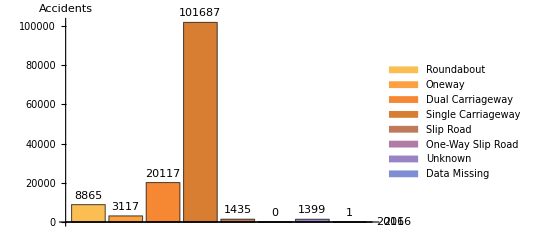

```mathematica
AccidentsRoadType2016=BarChart[{{Count[RoadT,{2016,1}],Count[RoadT,{2016,2}],Count[RoadT,{2016,3}],Count[RoadT,{2016,6}],Count[RoadT,{2016,7}],Count[RoadT,{2016,12}],Count[RoadT,{2016,9}],Count[RoadT,{2016,-1}]}},AxesLabel->{"2016","Accidents"},ChartLegends->{"Roundabout","Oneway","Dual Carriageway","Single Carriageway","Slip Road","One-Way Slip Road","Unknown","Data Missing"},LabelingFunction->(Placed[Row[{#}],Above]&)]
```

Road types of accidents in 2017 :

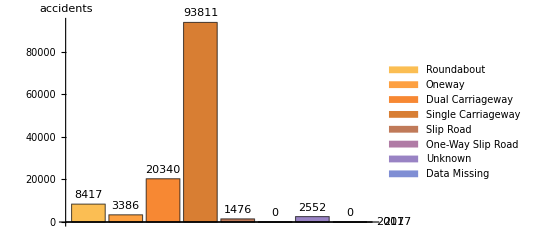

```mathematica
AccidentsRoadType2017=BarChart[{{Count[RoadT,{2017,1}],Count[RoadT,{2017,2}],Count[RoadT,{2017,3}],Count[RoadT,{2017,6}],Count[RoadT,{2017,7}],Count[RoadT,{2017,12}],Count[RoadT,{2017,9}],Count[RoadT,{2017,-1}]}},AxesLabel->{"2017","accidents"},ChartLegends->{{"Roundabout","Oneway","Dual Carriageway","Single Carriageway","Slip Road","One-Way Slip Road","Unknown","Data Missing"}},LabelingFunction->(Placed[Row[{#}],Above]&)]
```

Road types of accidents in 2018:

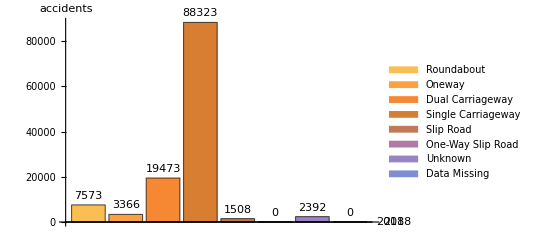

```mathematica
AccidentsRoadType2018=BarChart[{{Count[RoadT,{2018,1}],Count[RoadT,{2018,2}],Count[RoadT,{2018,3}],Count[RoadT,{2018,6}],Count[RoadT,{2018,7}],Count[RoadT,{2018,12}],Count[RoadT,{2018,9}],Count[RoadT,{2018,-1}]}},AxesLabel->{"2018","accidents"},ChartLegends->{{"Roundabout","Oneway","Dual Carriageway","Single Carriageway","Slip Road","One-Way Slip Road","Unknown","Data Missing"}},LabelingFunction->(Placed[Row[{#}],Above]&)]
```

Road types of accidents in 2019:

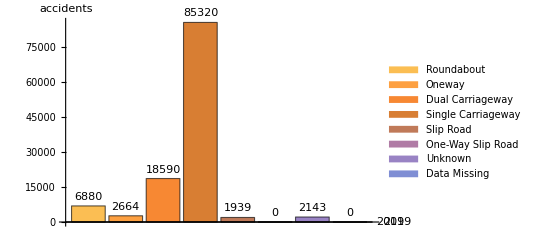

```mathematica
AccidentsRoadType2019=BarChart[{{Count[RoadT,{2019,1}],Count[RoadT,{2019,2}],Count[RoadT,{2019,3}],Count[RoadT,{2019,6}],Count[RoadT,{2019,7}],Count[RoadT,{2019,12}],Count[RoadT,{2019,9}],Count[RoadT,{2019,-1}]}},AxesLabel->{"2019","accidents"},ChartLegends->{{"Roundabout","Oneway","Dual Carriageway","Single Carriageway","Slip Road","One-Way Slip Road","Unknown","Data Missing"}},LabelingFunction->(Placed[Row[{#}],Above]&)]
```

Road types of accidents in 2020:

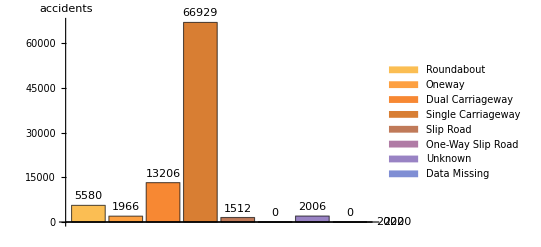

```mathematica
AccidentsRoadType2020=BarChart[{{Count[RoadT,{2020,1}],Count[RoadT,{2020,2}],Count[RoadT,{2020,3}],Count[RoadT,{2020,6}],Count[RoadT,{2020,7}],Count[RoadT,{2020,12}],Count[RoadT,{2020,9}],Count[RoadT,{2020,-1}]}},AxesLabel->{"2020","accidents"},ChartLegends->{{"Roundabout","Oneway","Dual Carriageway","Single Carriageway","Slip Road","One-Way Slip Road","Unknown","Data Missing"}},LabelingFunction->(Placed[Row[{#}],Above]&)]
```

### Severity and road type:

Fatal severity and type of road where the accident took place in all years:

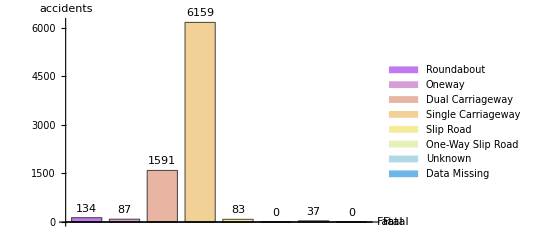

```mathematica
SeverityRoadAll=BarChart[{{Count[SeverityRoadType,{1,1}],Count[SeverityRoadType,{1,2}],Count[SeverityRoadType,{1,3}],Count[SeverityRoadType,{1,6}],Count[SeverityRoadType,{1,7}],Count[SeverityRoadType,{1,12}],Count[SeverityRoadType,{1,9}],Count[SeverityRoadType,{1,-1}]}},AxesLabel->{"Fatal","accidents"},LabelingFunction->(Placed[Row[{#}],Above]&),BarSpacing->Medium, ChartStyle->"Pastel",ChartLegends->{"Roundabout","Oneway","Dual Carriageway","Single Carriageway","Slip Road","One-Way Slip Road","Unknown","Data Missing"}]
```

Serious severity type of road where the accident took place in all years:

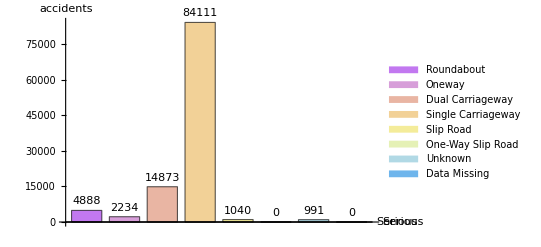

```mathematica
SeverityRoadAll=BarChart[{{Count[SeverityRoadType,{2,1}],Count[SeverityRoadType,{2,2}],Count[SeverityRoadType,{2,3}],Count[SeverityRoadType,{2,6}],Count[SeverityRoadType,{2,7}],Count[SeverityRoadType,{2,12}],Count[SeverityRoadType,{2,9}],Count[SeverityRoadType,{2,-1}]}},AxesLabel->{"Serious","accidents"},LabelingFunction->(Placed[Row[{#}],Above]&),BarSpacing->Medium, ChartStyle->"Pastel",ChartLegends->{"Roundabout","Oneway","Dual Carriageway","Single Carriageway","Slip Road","One-Way Slip Road","Unknown","Data Missing"}]
```

Slight  severity type of road where the accident took place in all years:

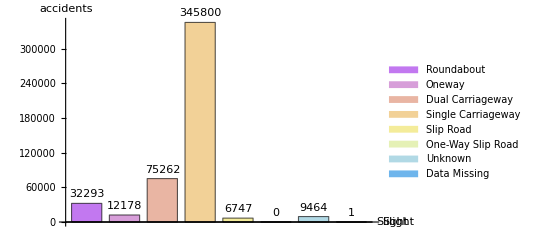

```mathematica
SeverityRoadAll=BarChart[{{Count[SeverityRoadType,{3,1}],Count[SeverityRoadType,{3,2}],Count[SeverityRoadType,{3,3}],Count[SeverityRoadType,{3,6}],Count[SeverityRoadType,{3,7}],Count[SeverityRoadType,{3,12}],Count[SeverityRoadType,{3,9}],Count[SeverityRoadType,{3,-1}]}},AxesLabel->{"Slight","accidents"},LabelingFunction->(Placed[Row[{#}],Above]&),BarSpacing->Medium, ChartStyle->"Pastel",ChartLegends->{"Roundabout","Oneway","Dual Carriageway","Single Carriageway","Slip Road","One-Way Slip Road","Unknown","Data Missing"}]
```

### Accident light condition

Light condition at the time of accident in all years 2016-2020:

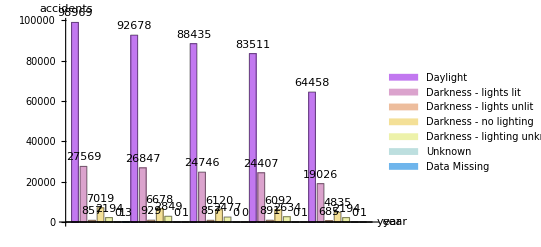

```mathematica
DuetoLightAll=BarChart[{{Count[DuetoLightC,{2016,1}],Count[DuetoLightC,{2016,4}],Count[DuetoLightC,{2016,5}],Count[DuetoLightC,{2016,6}],Count[DuetoLightC,{2016,7}],Count[DuetoLightC,{2016,9}],Count[DuetoLightC,{2016,-1}]},{Count[DuetoLightC,{2017,1}],Count[DuetoLightC,{2017,4}],Count[DuetoLightC,{2017,5}],Count[DuetoLightC,{2017,6}],Count[DuetoLightC,{2017,7}],Count[DuetoLightC,{2017,9}],Count[DuetoLightC,{2017,-1}]},{Count[DuetoLightC,{2018,1}],Count[DuetoLightC,{2018,4}],Count[DuetoLightC,{2018,5}],Count[DuetoLightC,{2018,6}],Count[DuetoLightC,{2018,7}],Count[DuetoLightC,{2018,9}],Count[DuetoLightC,{2018,-1}]},{Count[DuetoLightC,{2019,1}],Count[DuetoLightC,{2019,4}],Count[DuetoLightC,{2019,5}],Count[DuetoLightC,{2019,6}],Count[DuetoLightC,{2019,7}],Count[DuetoLightC,{2019,9}],Count[DuetoLightC,{2019,-1}]},{Count[DuetoLightC,{2020,1}],Count[DuetoLightC,{2020,4}],Count[DuetoLightC,{2020,5}],Count[DuetoLightC,{2020,6}],Count[DuetoLightC,{2020,7}],Count[DuetoLightC,{2020,9}],Count[DuetoLightC,{2020,-1}]}},AxesLabel->{"year","accidents"},ChartLegends->{"Daylight","Darkness - lights lit","Darkness - lights unlit","Darkness - no lighting","Darkness - lighting unknown","Unknown","Data Missing"},LabelingFunction->(Placed[Row[{#}],Above]&),BarSpacing->Medium, ChartStyle->"Pastel"]
```

Light conditions during the accident in 2016:

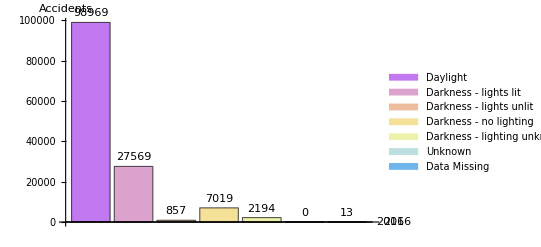

```mathematica
AccidentsLightCondition16=BarChart[{{Count[DuetoLightC,{2016,1}],Count[DuetoLightC,{2016,4}],Count[DuetoLightC,{2016,5}],Count[DuetoLightC,{2016,6}],Count[DuetoLightC,{2016,7}],Count[DuetoLightC,{2016,9}],Count[DuetoLightC,{2016,-1}]}},AxesLabel->{"2016","Accidents"},ChartLegends->{"Daylight","Darkness - lights lit","Darkness - lights unlit","Darkness - no lighting","Darkness - lighting unknown","Unknown","Data Missing"},LabelingFunction->(Placed[Row[{#}],Above]&), ChartStyle->"Pastel"]
```

Light conditions during the accident in 2017:

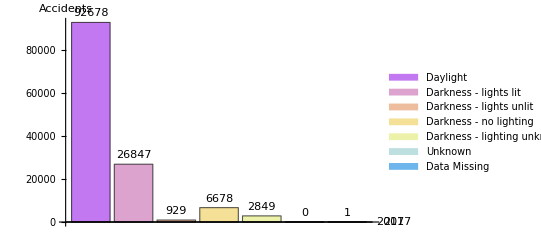

```mathematica
AccidentsLightCondition16=BarChart[{{Count[DuetoLightC,{2017,1}],Count[DuetoLightC,{2017,4}],Count[DuetoLightC,{2017,5}],Count[DuetoLightC,{2017,6}],Count[DuetoLightC,{2017,7}],Count[DuetoLightC,{2017,9}],Count[DuetoLightC,{2017,-1}]}},AxesLabel->{"2017","Accidents"},ChartLegends->{"Daylight","Darkness - lights lit","Darkness - lights unlit","Darkness - no lighting","Darkness - lighting unknown","Unknown","Data Missing"},LabelingFunction->(Placed[Row[{#}],Above]&), ChartStyle->"Pastel"]
```

Light conditions during the accident in 2018:

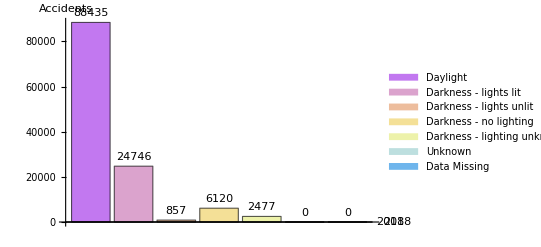

```mathematica
AccidentsLightCondition16=BarChart[{{Count[DuetoLightC,{2018,1}],Count[DuetoLightC,{2018,4}],Count[DuetoLightC,{2018,5}],Count[DuetoLightC,{2018,6}],Count[DuetoLightC,{2018,7}],Count[DuetoLightC,{2018,9}],Count[DuetoLightC,{2018,-1}]}},AxesLabel->{"2018","Accidents"},ChartLegends->{"Daylight","Darkness - lights lit","Darkness - lights unlit","Darkness - no lighting","Darkness - lighting unknown","Unknown","Data Missing"},LabelingFunction->(Placed[Row[{#}],Above]&), ChartStyle->"Pastel"]
```

Light conditions during the accident in 2019:

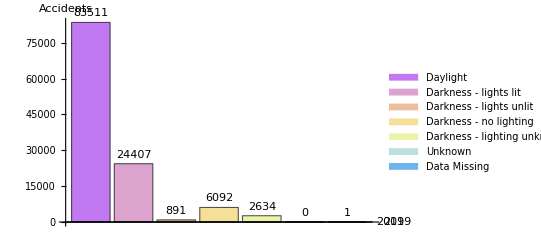

```mathematica
AccidentsLightCondition16=BarChart[{{Count[DuetoLightC,{2019,1}],Count[DuetoLightC,{2019,4}],Count[DuetoLightC,{2019,5}],Count[DuetoLightC,{2019,6}],Count[DuetoLightC,{2019,7}],Count[DuetoLightC,{2019,9}],Count[DuetoLightC,{2019,-1}]}},AxesLabel->{"2019","Accidents"},ChartLegends->{"Daylight","Darkness - lights lit","Darkness - lights unlit","Darkness - no lighting","Darkness - lighting unknown","Unknown","Data Missing"},LabelingFunction->(Placed[Row[{#}],Above]&), ChartStyle->"Pastel"]
```

Light conditions during the accident in 2020:

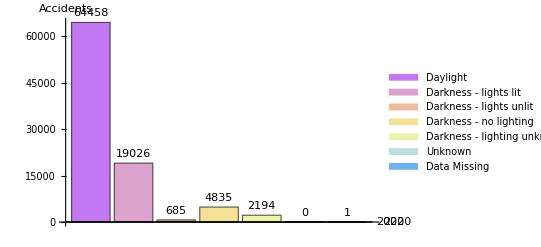

```mathematica
AccidentsLightCondition16=BarChart[{{Count[DuetoLightC,{2020,1}],Count[DuetoLightC,{2020,4}],Count[DuetoLightC,{2020,5}],Count[DuetoLightC,{2020,6}],Count[DuetoLightC,{2020,7}],Count[DuetoLightC,{2020,9}],Count[DuetoLightC,{2020,-1}]}},AxesLabel->{"2020","Accidents"},ChartLegends->{"Daylight","Darkness - lights lit","Darkness - lights unlit","Darkness - no lighting","Darkness - lighting unknown","Unknown","Data Missing"},LabelingFunction->(Placed[Row[{#}],Above]&), ChartStyle->"Pastel"]
```

### Severity based on light condition:

Fatal  severity based on type of light conditions where the accident took place in all years

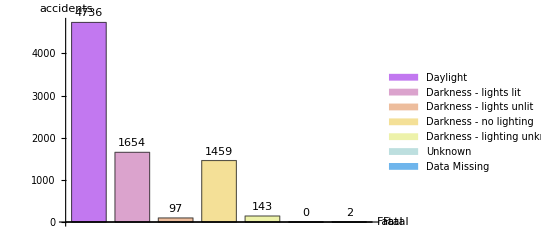

```mathematica
SeverityLightAll=BarChart[{{Count[SeverityLightC,{1,1}],Count[SeverityLightC,{1,4}],Count[SeverityLightC,{1,5}],Count[SeverityLightC,{1,6}],Count[SeverityLightC,{1,7}],Count[SeverityLightC,{1,9}],Count[SeverityLightC,{1,-1}]}},AxesLabel->{"Fatal","accidents"},LabelingFunction->(Placed[Row[{#}],Above]&),BarSpacing->Medium, ChartStyle->"Pastel",ChartLegends->{"Daylight","Darkness - lights lit","Darkness - lights unlit","Darkness - no lighting","Darkness - lighting unknown","Unknown","Data Missing"}]
```

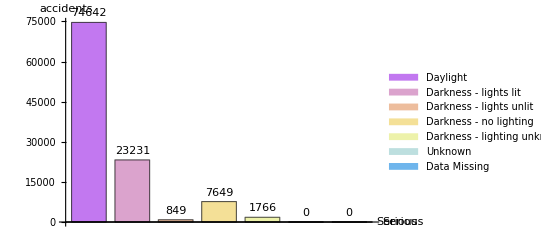

```mathematica
SeverityLightAll=BarChart[{{Count[SeverityLightC,{2,1}],Count[SeverityLightC,{2,4}],Count[SeverityLightC,{2,5}],Count[SeverityLightC,{2,6}],Count[SeverityLightC,{2,7}],Count[SeverityLightC,{2,9}],Count[SeverityLightC,{2,-1}]}},AxesLabel->{"Serious","accidents"},LabelingFunction->(Placed[Row[{#}],Above]&),BarSpacing->Medium, ChartStyle->"Pastel",ChartLegends->{"Daylight","Darkness - lights lit","Darkness - lights unlit","Darkness - no lighting","Darkness - lighting unknown","Unknown","Data Missing"}]
```

Serious  severity based on type of light conditions where the accident took place in all years

```mathematica
SeverityLightAll = BarChart[{{Count[SeverityLightC, {3, 1}], Count[SeverityLightC, {3, 4}], Count[SeverityLightC, {3, 5}], Count[SeverityLightC, {3, 6}], Count[SeverityLightC, {3, 7}], Count[SeverityLightC, {3, 9}], Count[SeverityLightC, {3, -1}]}}, AxesLabel -> {"Slight", "accidents"}, LabelingFunction -> (Placed[Row[{#}], Above] &), BarSpacing -> Medium, ChartStyle -> "Pastel", ChartLegends -> {"Daylight", "Darkness - lights lit", "Darkness - lights unlit", "Darkness - no lighting", "Darkness - lighting unknown", "Unknown", "Data Missing"}]
```

Slight  severity based on type of light conditions where the accident took place in all years

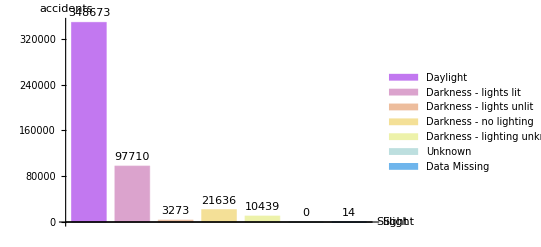

### Day of week

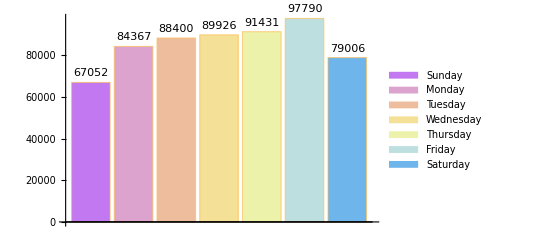

```mathematica
daysoftheweekbar=BarChart[{Count[daysoftheweek,1],Count[daysoftheweek,2],Count[daysoftheweek,3],Count[daysoftheweek,4],Count[daysoftheweek,5],Count[daysoftheweek,6],Count[daysoftheweek,7]},LabelingFunction->(Placed[Row[{#}],Above]&),ChartStyle->"Pastel",ChartLegends->{"Sunday","Monday","Tuesday","Wednesday","Thursday","Friday","Saturday"}]
```

## Short term analysis

#### Descriptive statistics

Checking the total number of accidents in years 2016-2020 by selecting column accident_year from the dataset:

```mathematica
totalaccidents=fullaccidents[[;;597974, 2]];
```

```mathematica
Length[totalaccidents]
```

597973

Counting accidents in each year:

```mathematica
total2016=Count[totalaccidents, 2016]
```

136621

```mathematica
total2017=Count[totalaccidents, 2017]
```

129982

```mathematica
total2018=Count[totalaccidents, 2018]
```

122635

```mathematica
total2019=Count[totalaccidents, 2019]
```

117536

```mathematica
total2020=Count[totalaccidents,2020]
```

91199

Checking that there are no missing years in the data:

```mathematica
Total[{total2016,total2017, total2018, total2019, total2020}]
```

597973

### Chart 2016-2020

Displaying the number of accidents in years 2016-2020 as a bar chart:

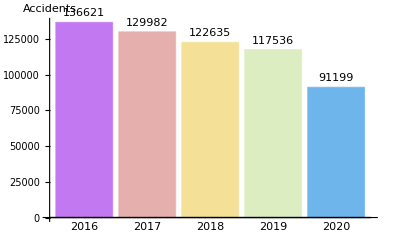

```mathematica
plottotals2=BarChart[{total2016,total2017,total2018,total2019,total2020},ChartLabels->Placed[{"2016", "2017","2018","2019","2020"},Below],AxesLabel->{None,Accidents},ChartStyle->"Pastel",LabelingFunction->(Placed[Row[{#}],Above]&)]
```

There is a noticeable drop in the number of accidents in 2020.

### Plots 2019 and 2020

Joined plot for number of accidents in 2019 and 2020 :

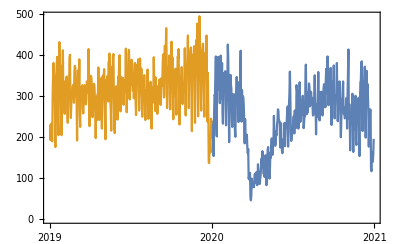

```mathematica
combined=DateListPlot[{dailyaccidents2020,dailyaccidents2019}]
```

### Data analysis

#### Comparing the first 85 days in 2020 (before lockdown) to the 85 days after lockdown started on March 26th:

Calculating mean and standard deviation:

```mathematica
meanfirst85in2020=Mean[first85in2020]//N
```

284.953

```mathematica
StandardDeviation[first85in2020]//N
```

71.4281

```mathematica
meansecond85in2020=Mean[second85in2020]//N
```

153.447

```mathematica
StandardDeviation[second85in2020]//N
```

55.2159

Running an independent samples t - test to analyse whether there was a significant difference in the number of car accidents between the first 85 days of 2020 and the 85 days after lockdown in 2020:

```mathematica
TTest[{first85in2020,second85in2020},Automatic,"TestDataTable"]
```

| Statistic | P-Value
T | 13.4294 | 6.48089×10^-28

There was a significant difference.

#### Comparing the first 85 days in 2020 to the first 85 days in 2019 to compare the same time periods in 2 different years before lockdown measures.

```mathematica
meanfirst85in2019=Mean[first85in2019]//N
```

306.048

```mathematica
StandardDeviation[first85in2019]//N
```

55.9335

```mathematica
meanfirst85in2020
```

284.953

```mathematica
StandardDeviation[first85in2020]//N
```

71.4281

Running an independent samples t-test to look for a significant difference between first 85 days of 2019 and 2020:

```mathematica
TTest[{first85in2020,first85in2019},Automatic,"TestDataTable"]
```

| Statistic | P-Value
T | -2.13889 | 0.0339741

#### Comparing the 85 days after March 26th in 2020 (post lockdown) and 2019 by using a t-test (as used above) to see if there was a significant difference between the means:

```mathematica
meansecond85in2019=Mean[second85in2019]//N
```

310.976

```mathematica
StandardDeviation[second85in2019]//N
```

49.3775

```mathematica
meansecond85in2020
```

153.447

```mathematica
StandardDeviation[second85in2020]//N
```

55.2159

```mathematica
TTest[{second85in2020,second85in2019},Automatic,"TestDataTable"]
```

| Statistic | P-Value
T | -19.6068 | 2.76222×10^-45

#### Bar chart

Bar chart showing the mean number of accidents in the first 85 days of 2019 and 2020, and the mean number of accidents in the 85 days after March 26th in 2019 and 2020, where in 2020 that was the day lockdown was introduced .

```mathematica
BarChart[{{meanfirst85in2019,meanfirst85in2020},{meansecond85in2019,Callout[meansecond85in2020,"after lockdown"]}}, ChartLabels->{Placed[{"first 84/85 days","85 days after March 26th"},Below],Placed[{"2019", "2020"},Above]},AxesLabel->{ None,"Mean number of car accidents"},
ColorFunction->Automatic, ChartStyle->"Pastel"]
```

-Graphics-

-Graphics-

#### To gain a larger perspective, looking at the first 85 days and the 85 days after March 26th for the years 2016-2020.

Looking at the mean number of accidents in the early days of the year in years 2016 - 2020:

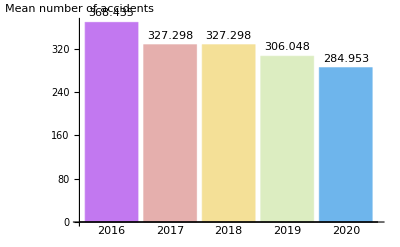

```mathematica
BarChart[{mean2016first,mean2017first,mean2018first,meanfirst85in2019,meanfirst85in2020},ChartLabels->Placed[{"2016","2017","2018","2019","2020"},Below],ColorFunction->Automatic,ChartStyle->"Pastel",AxesLabel-> {None, "Mean number of accidents"},LabelingFunction->(Placed[Row[{#}],Above]&)]
```

Looking at the mean number of accidents in the 85 days after March 26th in years 2019-2020.

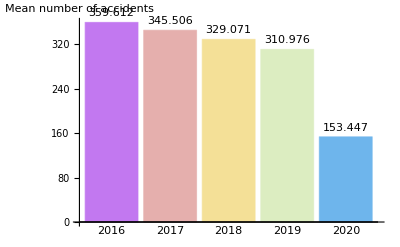

```mathematica
BarChart[{mean2016,mean2017,mean2018,meansecond85in2019,meansecond85in2020},ChartLabels->Placed[{"2016","2017","2018","2019","2020"},Below],ColorFunction->Automatic,ChartStyle->"Pastel",AxesLabel-> {None, "Mean number of accidents"},LabelingFunction->(Placed[Row[{#}],Above]&)]
```